## BC20 error

```mathematica
raw = Import["/Users/nmajik/twiss_results_patch.json"];
raw = Association[#]&/@raw;

data = GroupBy[raw,#energy&]
```

```mathematica
selectedEnergies = {9.0*^9, 9.9*^9, 10.0*^9, 10.1*^9, 11.0*^9}
colors = Table[
ColorData["Rainbow"][Rescale[i,{1,Length[selectedEnergies]}]],
{i,Length[selectedEnergies]}
]
```

{9.×10^9,9.9×10^9,1.×10^10,1.01×10^10,1.1×10^10}

{RGBColor[0.471412, 0.108766, 0.527016],RGBColor[0.266122, 0.486664, 0.802529],RGBColor[0.513417, 0.72992, 0.440682],RGBColor[0.863512, 0.670771, 0.236564],RGBColor[0.857359, 0.131106, 0.132128]}

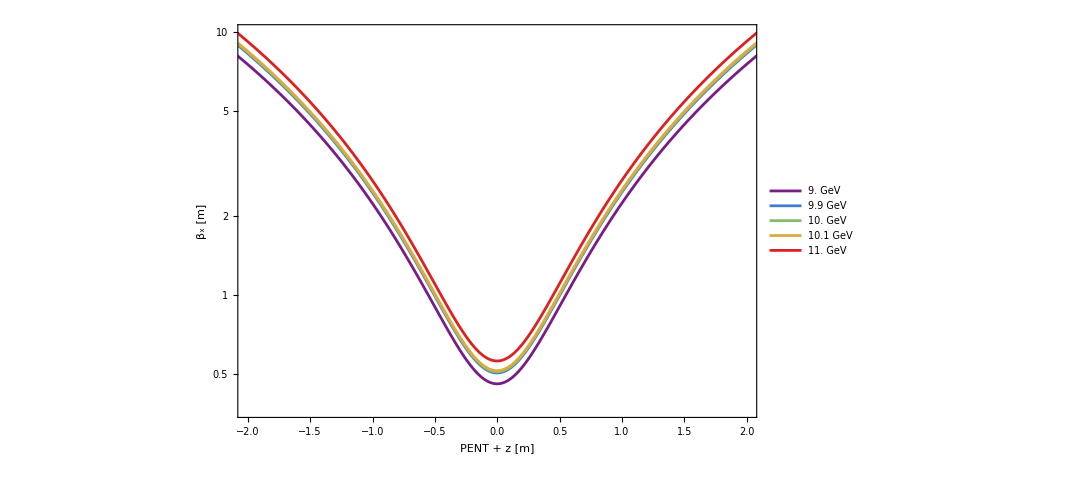

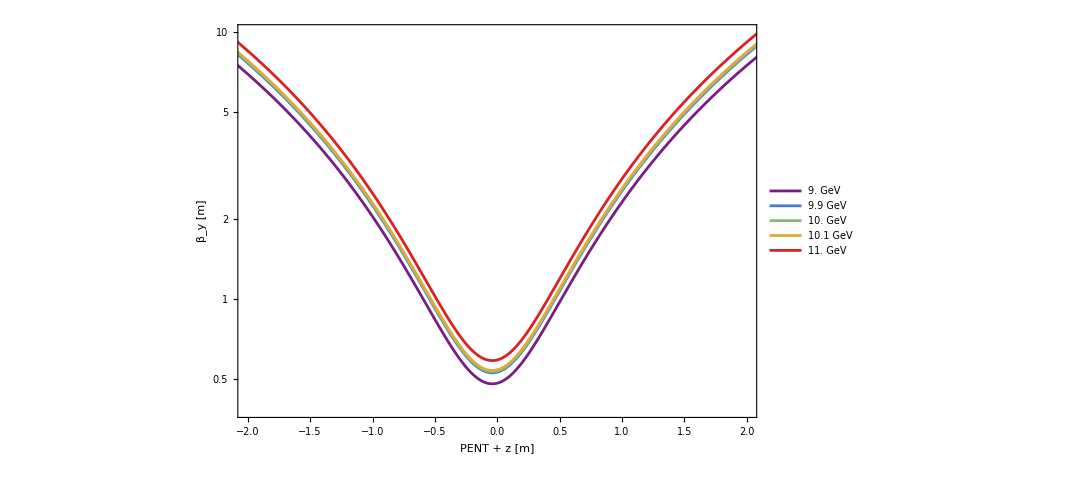

```mathematica
ListLogPlot[
Table[
{#s,#betaX}&/@data[key],
{key,selectedEnergies}
],
Joined->True,
ImageSize->800,
Frame->True,
LabelStyle->20,
PlotRange->{{-2,2},{All,10}},
FrameLabel->{"PENT + z [m]","β_x [m]"},
PlotLegends->((ToString[#/10^9]<>" GeV" )&/@selectedEnergies),
PlotStyle->colors
]
ListLogPlot[
Table[
{#s,#betaY}&/@data[key],
{key,selectedEnergies}
],
Joined->True,
ImageSize->800,
Frame->True,
LabelStyle->20,
PlotRange->{{-2,2},{All,10}},
FrameLabel->{"PENT + z [m]","β_y [m]"},
PlotLegends->((ToString[#/10^9]<>" GeV" )&/@selectedEnergies),
PlotStyle->colors
]
```

## L3 error

```mathematica
raw = Import["/Users/nmajik/twiss_results_L3.json"];
raw = Association[#]&/@raw;

data = GroupBy[raw,#L3Voltage&]
```

```mathematica
selectedEnergies = 10^9{5.3,5.4, 5.5,5.6,5.7}
selectedEnergies =Keys[data]
colors = Table[
ColorData["Rainbow"][Rescale[i,{1,Length[selectedEnergies]}]],
{i,Length[selectedEnergies]}
]
```

{5.3×10^9,5.4×10^9,5.5×10^9,5.6×10^9,5.7×10^9}

{4.5×10^9,4.6×10^9,4.7×10^9,4.8×10^9,4.9×10^9,5.×10^9,5.1×10^9,5.2×10^9,5.3×10^9,5.4×10^9,5.5×10^9,5.6×10^9,5.7×10^9,5.8×10^9,5.9×10^9,6.×10^9,6.1×10^9,6.2×10^9,6.3×10^9,6.4×10^9,6.5×10^9}

{RGBColor[0.471412, 0.108766, 0.527016],RGBColor[0.3431304, 0.11581720000000001, 0.6369784000000001],RGBColor[0.2748608, 0.1822636, 0.7272788],RGBColor[0.2480688, 0.2797284, 0.7879248],RGBColor[0.2484884, 0.3863264, 0.813373],RGBColor[0.266122, 0.486664, 0.802529],RGBColor[0.2979596, 0.5657928, 0.7522386000000001],RGBColor[0.3386556, 0.6276854, 0.6832816],RGBColor[0.38822480000000004, 0.674195, 0.6035436000000001],RGBColor[0.446557, 0.7074632, 0.5203932],RGBColor[0.513417, 0.72992, 0.440682],RGBColor[0.5888042, 0.7409584, 0.37500680000000003],RGBColor[0.6660832000000001, 0.7430418, 0.32293540000000004],RGBColor[0.7408424, 0.7340177999999999, 0.2838318],RGBColor[0.8083416, 0.7110806, 0.255976],RGBColor[0.863512, 0.670771, 0.236564],RGBColor[0.8935136, 0.6004149999999999, 0.2205464],RGBColor[0.9021174, 0.5055088, 0.2018252],RGBColor[0.8929546, 0.3896616, 0.1794008],RGBColor[0.8739574, 0.2607876, 0.15481040000000001],RGBColor[0.857359, 0.131106, 0.132128]}

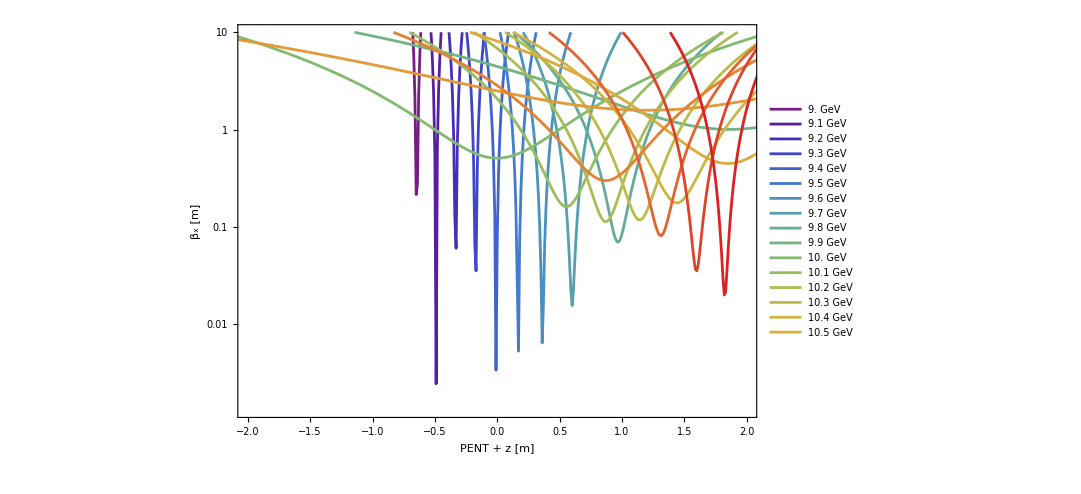

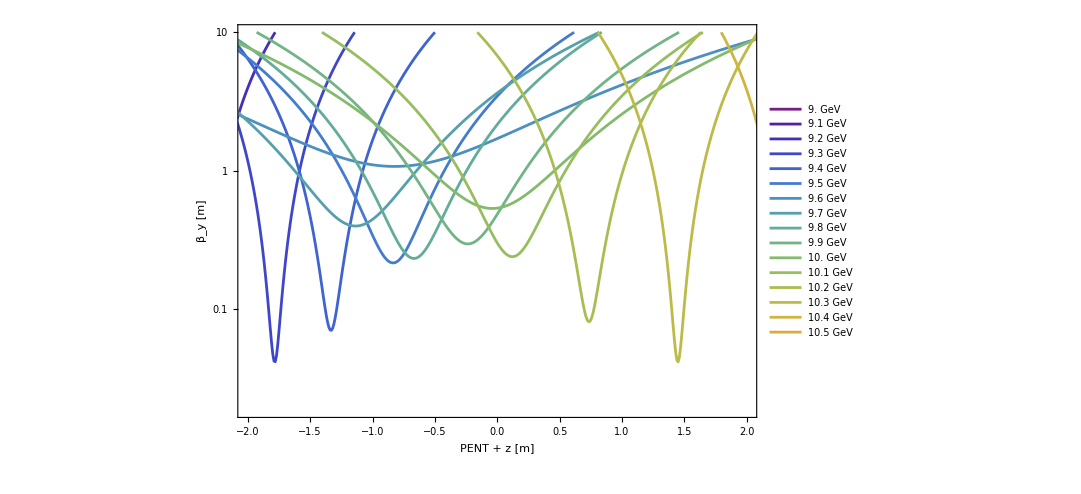

```mathematica
ListLogPlot[
Table[
{#s,#betaX}&/@data[key],
{key,selectedEnergies}
],
Joined->True,
ImageSize->800,
Frame->True,
LabelStyle->20,
PlotRange->{{-2,2},{All,10}},
FrameLabel->{"PENT + z [m]","β_x [m]"},
PlotLegends->((ToString[#/10^9+4.5]<>" GeV" )&/@selectedEnergies),
PlotStyle->colors
]
ListLogPlot[
Table[
{#s,#betaY}&/@data[key],
{key,selectedEnergies}
],
Joined->True,
ImageSize->800,
Frame->True,
LabelStyle->20,
PlotRange->{{-2,2},{All,10}},
FrameLabel->{"PENT + z [m]","β_y [m]"},
PlotLegends->((ToString[#/10^9+4.5]<>" GeV" )&/@selectedEnergies),
PlotStyle->colors
]
```